Моделиране нивото на въглеродния диоксид в атмосферата

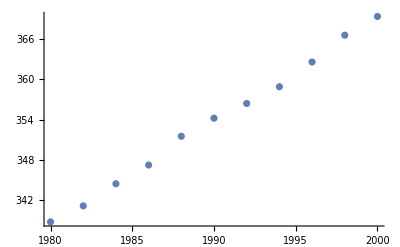

```mathematica
data = {{1980,338.7},{1982,341.1},{1984,344.4},{1986,347.2},{1988,351.5},{1990,354.2},{1992,356.4},{1994,358.9},{1996,362.6},{1998,366.6},{2000,369.4}};
plot1=ListPlot[data,PlotRange->All]
p[x_]:=InterpolatingPolynomial[data,x]
pp=Plot[p[x],{x,1980,2000},PlotStyle->Red];
Show[plot1,pp,PlotRange->All];
```

Приближаване стойността на функцията f(x)=sin x, за x = π/5

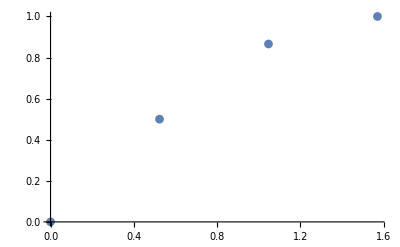

```mathematica
dataSin={{0,Sin[0]},{π/6,Sin[π/6]},{π/3,Sin[π/3]},{π/2,Sin[π/2]}};
pSin[x_]:=InterpolatingPolynomial[dataSin,x]
pp2=Plot[pSin[x],{x,0,Pi/2},PlotStyle->Red];
plot2=ListPlot[dataSin,PlotRange->All,PlotMarkers->Automatic]
Show[pp2,plot2];
```

Зад. 1  Даден е алгебричният полином:
p(x)= 512+2304 x-4608 x^2+5376 x^3-4032 x^4+2016 x^5-672 x^6+144 x^7-18 x^8+x^9
Да се построи неговата графика в интервала  [ 1.9,2.1] , като за пресмятане на стойностите му се използва:
a) (x-2)^9 ;
	     б) 512+2304 x-4608 x^2+5376 x^3-4032 x^4+2016 x^5-672 x^6+144 x^7-18 x^8+x^9

Зад. 2 Като се използва интерполационната формула на Лагранж да се намери полином P(x) ∈ π_3,който удовлетворява условията:
P(1) =2; P(2) =9; P(4) =41, P(6) = 97.